## Compute k

```mathematica
gamma1 = 4.13;
gamma2 = 8.43;
l1=0.9;
l2 =0.95;
Ceiling[gamma1/(1-l1)-1]
Ceiling[gamma1/(1-l2)-1]
Ceiling[gamma2-1+Sqrt[-Log[1-l1]*2(gamma2+1)^2]]
Ceiling[gamma2-1+Sqrt[-Log[1-l2]*2(gamma2+1)^2]]
```

## Plot Trajectories

### circuit

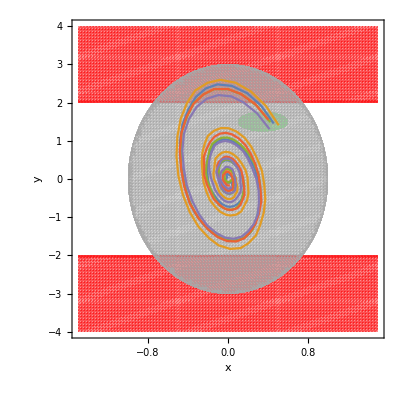

```mathematica
varSet = {x, y};
varRange = {{-1.5,1.5},{-4,4}}; 
flowVec = {8/9*x-1/18*y, x+y}; 
flowDist [x_]:={8/9*x[[1]]-1/18*x[[2]]+0.01*RandomVariate[UniformDistribution[{-1,1}]],x[[1]]+x[[2]]} 
(*+d for disturbance, uniform distribution [-1,1]*)
unsafeBoundary = {4-y^2};
initBoundary = {(x-0.35)^2+(y-1.5)^2-0.25^2};
domainBoundary = {9x^2+y^2-3^2};
ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];

flowPlot =VectorPlot[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];

initCons=And@@Thread[LessEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[LessEqualThan[0][unsafeBoundary]];
domainCons=And@@Thread[LessEqualThan[0][domainBoundary]];

initPlot=RegionPlot[initCons,Evaluate[ranges],PlotStyle->{Opacity[.8],,RGBColor[0.5,0.96,0.53]},BoundaryStyle->None ,PlotPoints-> 100(*,PlotLegends->SwatchLegend[{""}]*)];
unsafePlot=RegionPlot[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[.5],RGBColor[0.99,0.1,0.11]},BoundaryStyle->None,PlotPoints-> 100(*,PlotLegends->SwatchLegend[{""}]*)];
domainPlot=RegionPlot[domainCons,Evaluate[ranges],PlotStyle->{Opacity[.5],RGBColor[0.66,0.66,0.66]},BoundaryStyle->None,PlotPoints-> 100(*,PlotLegends->SwatchLegend[{""}]*)];
initSamples = RandomPoint[ImplicitRegion[initCons,{x,y}],5];
trajGen[x_]:= NestList[flowDist,x,100];
trajTable = Map[trajGen,initSamples];
trajPlot = ListLinePlot[trajTable];
Show[initPlot,unsafePlot,domainPlot,trajPlot,FrameLabel->{x,y}]
```

### vanderpol

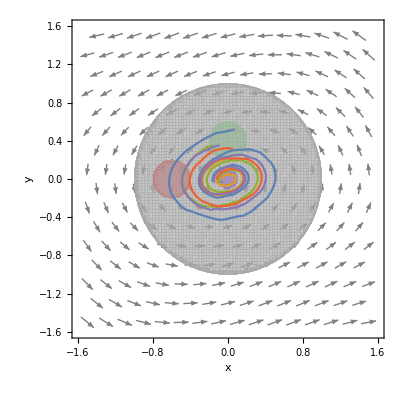

```mathematica
varSet = {x, y};
varRange = {{-1.5,1.5},{-1.5,1.5}}; 
flowVec = {-2*y, x+0.5*(x^2-1)*y}; 
flowDist [x_]:={x[[1]]-0.1*2*x[[2]], x[[2]]+0.1*(x[[1]]+0.5*(x[[1]]^2-1-RandomVariate[UniformDistribution[{-1,1}]])*x[[2]])} ;

(*+d for disturbance, uniform distribution [-1,1]*)
initBoundary = {x^2+(y-0.4)^2-0.2^2};
unsafeBoundary = {(x+0.6)^2+y^2-0.2^2};
targetBoundary = {x^2+y^2-0.1^2};
domainBoundary = {x^2+y^2-1^2};

ranges=Sequence @@ MapThread[Prepend,{varRange,varSet}];

flowPlot =VectorPlot[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];

initCons=And@@Thread[LessEqualThan[0][initBoundary]];
unsafeCons=And@@Thread[LessEqualThan[0][unsafeBoundary]];
targetCons=And@@Thread[LessEqualThan[0][targetBoundary]];
domainCons=And@@Thread[LessEqualThan[0][domainBoundary]];

initPlot=RegionPlot[initCons,Evaluate[ranges],PlotStyle->{Opacity[.8],,RGBColor[0.5,0.96,0.53]},BoundaryStyle->None ,PlotPoints-> 100,PlotLegends->SwatchLegend[{""}]];
unsafePlot=RegionPlot[unsafeCons,Evaluate[ranges],PlotStyle->{Opacity[.5],RGBColor[0.99,0.1,0.11]},BoundaryStyle->None,PlotPoints-> 100,PlotLegends->SwatchLegend[{""}]];
targetPlot=RegionPlot[targetCons,Evaluate[ranges],PlotStyle->{Opacity[.5],RGBColor[0.48,0.,0.92,0.5]},BoundaryStyle->None,PlotPoints-> 100,PlotLegends->SwatchLegend[{""}]];
domainPlot=RegionPlot[domainCons,Evaluate[ranges],PlotStyle->{Opacity[.5],RGBColor[0.66,0.66,0.66]},BoundaryStyle->None,PlotPoints-> 100,PlotLegends->SwatchLegend[{""}]];
initSamples = RandomPoint[ImplicitRegion[initCons,{x,y}],5];
trajGen[x_]:= NestList[flowDist,x,100];
trajTable = Map[trajGen,initSamples];
trajPlot = ListLinePlot[trajTable];
Show[flowPlot,initPlot,unsafePlot,targetPlot,domainPlot,trajPlot,FrameLabel->{x,y}]
```

### randomwalk

```mathematica
Show[flowPlot,initPlot,unsafePlot,targetPlot,domainPlot,trajPlot,FrameLabel->{x,y}]
```